```mathematica
(*Density response function*)
```

```mathematica
γ=1;
DT=1;
DS=1;
c=1;
L=1;
T=1;
```

```mathematica
χnF[ω_,k_,c_,γ_,DT_,Ds_]:=k^2*(-ω-I*k^2*γ*DT)/((ω^2-c^2*k^2+I*Ds*k^2*ω)*(ω+I*DT*k^2));
```

```mathematica
N[χnF[2,2,2,2,2,2]]
```

0.195294+0.338824 ⅈ

```mathematica
V[z_,s_,t_]=Exp[-z^2/(2*s^2)]*(2+Sin[t])+2*Exp[-(z-100)^2/(2*s^2)];
```

```mathematica
Manipulate[Plot[V[z,s,t],{z,0,100},PlotRange->{0,3}],{s,0.1,5},{t,0,10}]
```

General::munfl: Exp[-499980.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-970.288] is too small to represent as a normalized machine number; precision may be lost.

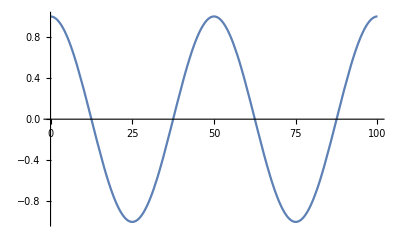

```mathematica
Plot[Cos[4*Pi*x/100],{x,0,100}]
```

```mathematica
180/18000
```

1/100

```mathematica
χ[w_,k_,c_,Ds_]:=Ds/((w-c*k)^2+Ds);
```

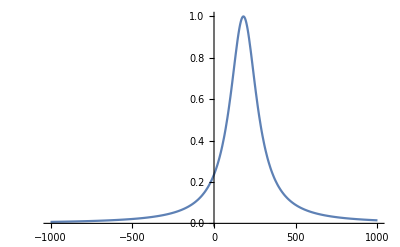

```mathematica
Plot[χ[w,0.01,18000,10000],{w,-1000,1000},PlotRange->All]
```

```mathematica
Manipulate[Plot[χ[w,k,18000,10000],{w,0,1000},PlotRange->Full],{k,0,0.05}]
```